```mathematica
ClearAll["Global`*"]
(*momenta parameters*)
ϕ1[ϕ_,el_,dl_]:=ArcSin[2*(dl)*(1/(el))+Sin[ϕ]]
(*py[ϕ_]:=ϵ*Sin[ϕ]+(d/(lb)^2)*)
px[ϕ_]:=Cos[ϕ]
px1[ϕ_,el_,dl_]:=Cos[ArcSin[2*(dl)*(1/(el))+Sin[ϕ]]]
(*Operators u*)
u1p[ϕ_,el_,dl_]:=ParabolicCylinderD[(((el)^2)/2)-1,Sqrt[2]*((-dl)+el*Sin[ϕ]+dl)] 
u1m[ϕ_,el_,dl_]:=ParabolicCylinderD[(((el)^2)/2)-1,-1*Sqrt[2]*((-dl)+el*Sin[ϕ]+dl)]
u2p[ϕ_,el_,dl_]:=ParabolicCylinderD[(((el)^2)/2)-1,Sqrt[2]*((dl)+el*Sin[ϕ]+dl)]
u2m[ϕ_,el_,dl_]:=ParabolicCylinderD[(((el)^2)/2)-1,-1*Sqrt[2]*((dl)+el*Sin[ϕ]+dl)]
(*Operators v*)
v1p[ϕ_,el_,dl_]:=ParabolicCylinderD[((el)^2)/2,Sqrt[2]*((-dl)+el*Sin[ϕ]+dl)]
v1m[ϕ_,el_,dl_]:=ParabolicCylinderD[((el)^2)/2,-1*Sqrt[2]*((-dl)+el*Sin[ϕ]+dl)]
v2p[ϕ_,el_,dl_]:=ParabolicCylinderD[((el)^2)/2,Sqrt[2]*((dl)+el*Sin[ϕ]+dl)]
v2m[ϕ_,el_,dl_]:=ParabolicCylinderD[((el)^2)/2,-1*Sqrt[2]*((dl)+el*Sin[ϕ]+dl)]
(*T[ϕ_]:=(8*((3.7)^4)*Cos[ϕ1[ϕ]]*Cos[ϕ]*((u2p[ϕ]*v2m[ϕ]+v2p[ϕ]*u2m[ϕ])^2))*)
(*D operator*)
Dop[ϕ_,el_,dl_]:=((el)^2)*Exp[I*(ϕ1[ϕ,el,dl]-ϕ)]*(u1p[ϕ,el,dl]*u2m[ϕ,el,dl]-u2p[ϕ,el,dl]*u1m[ϕ,el,dl])-2*(v1p[ϕ,el,dl]*v2m[ϕ,el,dl]-v2p[ϕ,el,dl]*v1m[ϕ,el,dl])+I*Sqrt[2]*el*(Exp[I*ϕ1[ϕ,el,dl]]*(v1p[ϕ,el,dl]*u2m[ϕ,el,dl]+u2p[ϕ,el,dl]*v1m[ϕ,el,dl])+Exp[-I*ϕ]*(u1p[ϕ,el,dl]*v2m[ϕ,el,dl]+v2p[ϕ,el,dl]*u1m[ϕ,el,dl]))
(*transmission amplitude*)
t[ϕ_,el_,dl_]:=(2*I*el*(u2p[ϕ,el,dl]*v2m[ϕ,el,dl]+v2p[ϕ,el,dl]*u2m[ϕ,el,dl]))/(Exp[I*(px[ϕ]+px1[ϕ,el,dl])*el*dl]*Dop[ϕ,el,dl])

(*Sqrt[2*px1[ϕ,el,dl]/px[ϕ]]*Cos[ϕ]*)
(*(2*I*3.7*Sqrt[2*px1[Pi/2,3.7,0.5]/px[Pi/2]]*Cos[Pi/2]*(u2p[Pi/2,3.7,0.5]*v2m[Pi/2,3.7,0.5]+v2p[Pi/2,3.7,0.5]*u2m[Pi/2,3.7,0.5]))
(Exp[I*(px[Pi/2]+px1[Pi/2,3.7,0.5])*3.7*0.5]*Dop[Pi/2,3.7,0.5])
Sqrt[2*px1[Pi/2,3.7,0.5]/px[Pi/2]]*)
(*px1[Pi/2,3.7,0.5]
px[Pi/2]*)
```

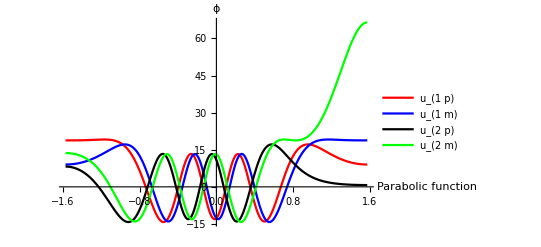

```mathematica
Plot[{u1p[ϕ,3.7,0.5],u1m[ϕ,3.7,0.5],u2p[ϕ,3.7,0.5],u2m[ϕ,3.7,0.5]},{ϕ,-Pi/2,Pi/2}, PlotStyle->{Red, Blue, Black, Green}, AxesLabel->{"Parabolic function","ϕ"},PlotLegends->{"u_(1  p)","u_(1  m)","u_(2  p)","u_(2  m)"}]
```

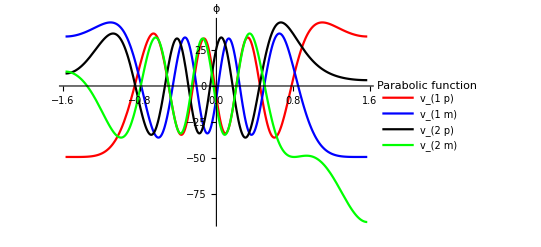

```mathematica
Plot[{v1p[ϕ,3.7,0.5],v1m[ϕ,3.7,0.5],v2p[ϕ,3.7,0.5],v2m[ϕ,3.7,0.5]},{ϕ,-Pi/2,Pi/2}, PlotStyle->{Red, Blue, Black, Green}, AxesLabel->{"Parabolic function","ϕ"},PlotLegends->{"v_(1  p)","v_(1  m)","v_(2  p)","v_(2  m)"}]
```

```mathematica
(*transmission equation*)
T[ϕ_,el_,dl_]:=2*px1[ϕ,el,dl]*Cos[ϕ]*t[ϕ,el,dl]*(t[ϕ,el,dl])*
```

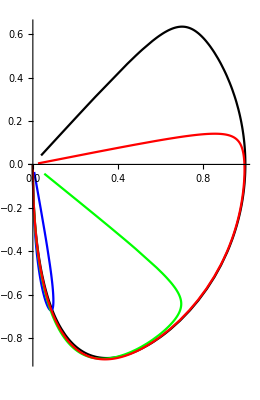

```mathematica
PolarPlot[{T[ϕ,3.7,0.5],T[ϕ,3.7,3.67],T[ϕ,3.7,3],T[ϕ,3.7,1.5]},{ϕ,-Pi/2,Pi/2}, PlotStyle->{Black,Blue,Green,Red}]
```

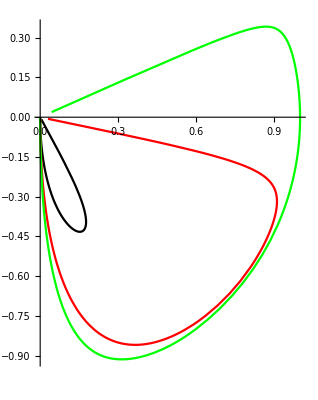

```mathematica
PolarPlot[{T[ϕ,1.6,1.5],T[ϕ,2.5,1.5],T[ϕ,5,1.5]},{ϕ,-Pi/2,Pi/2}, PlotStyle->{Black,Red,Green}]
```

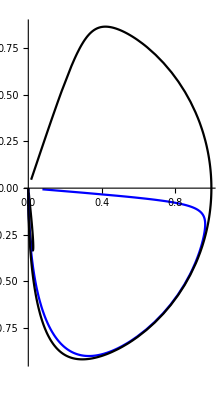

```mathematica
PolarPlot[{T[ϕ,3.7,3.69],T[ϕ,3.7,2.0],T[ϕ,3.7,0.1]},{ϕ,-Pi/2,Pi/2}, PlotStyle->{Black,Blue}]
```

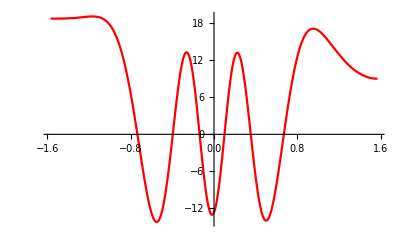

```mathematica
Plot[u1p[ϕ,3.7,0.5],{ϕ,-Pi/2,Pi/2}, PlotStyle->Red]
```